```mathematica
GFunction[numNodes_, numEdges_] := Graph[Table[RandomInteger[numNodes]->RandomInteger[numNodes],numEdges],VertexLabels->All]
MultipleGFunction[numNodes_, numEdges_, numGraphs_] :=Table[Graph[GFunction[numNodes,numEdges]],numGraphs]
CGraph[numNodes_, numEdges_] := CommunityGraphPlot[GFunction[numNodes, numEdges]]

Graph[1->2, 2->3, 3->1]
```

Graph::optrs: Option specification 3→1 in Graph[1→2,2→3,3→1] is not a rule for a symbol or string.

Graph[1→2,2→3,3→1]

```mathematica
Graph[{1->2,2->3,3->1, 4, 5, 6, 7}]
```

```mathematica
Graph[{1->2,2->3,3->1,4,5,6,7}]
```

```mathematica
Graph[{1->2,2->3,3->1,4->5,5->4,6->7,7->4, 7->1}]
```

-Graphics-

```mathematica
AdjacencyMatrix[Graph[{1, 2, 3, 4, 5, 6, 7}, {DirectedEdge[1, 2], DirectedEdge[2, 3], DirectedEdge[3, 1], DirectedEdge[4, 5], DirectedEdge[5, 4], DirectedEdge[6, 7], DirectedEdge[7, 4], DirectedEdge[7, 1]}]]
```

SparseArray[…]

```mathematica
VertexList[Graph[{1, 2, 3, 4, 5, 6, 7}, {DirectedEdge[1, 2], DirectedEdge[2, 3], DirectedEdge[3, 1], DirectedEdge[4, 5], DirectedEdge[5, 4], DirectedEdge[6, 7], DirectedEdge[7, 4], DirectedEdge[7, 1]}]]
```

{1,2,3,4,5,6,7}

```mathematica
Reverse[{1,2,3,4,5,6,7}]
```

{7,6,5,4,3,2,1}

```mathematica
Mean[{7,6,5,4,3,2,1}]
```

4

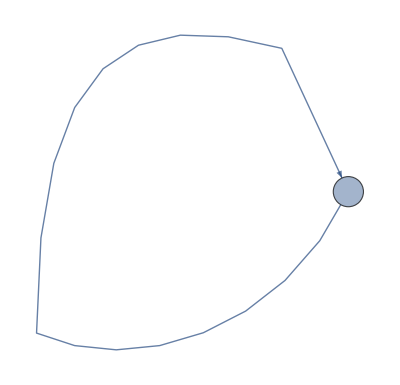

```mathematica
Graph[{1->1}]
```

```mathematica
VertexList[Graph[{1}, {DirectedEdge[1, 1]}]]
```

{1}

```mathematica
Graph[{1--2}]
```

Decrement::rvalue: 1 is not a variable with a value, so its value cannot be changed.

Graph[{2 1--}]

```mathematica
Table[i->j,{i,3},{j,3}]
```

{{1→1,1→2,1→3},{2→1,2→2,2→3},{3→1,3→2,3→3}}

```mathematica
Graph[Out[51]]
```

Graph[{{1→1,1→2,1→3},{2→1,2→2,2→3},{3→1,3→2,3→3}}]

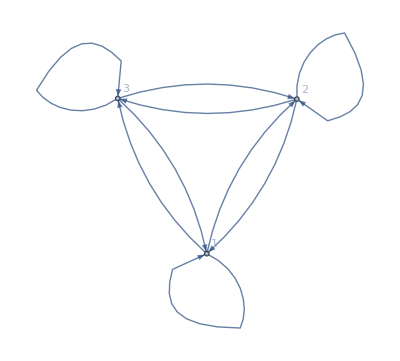

```mathematica
Graph[Flatten[Out[51]], VertexLabels->"Name"]
```

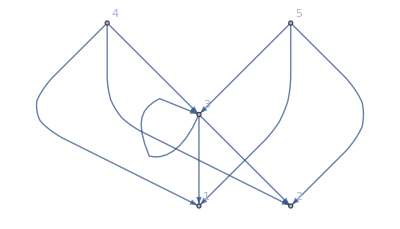

```mathematica
Graph[Flatten[Table[i->j, {i, 3,5}, {j, 3}]], VertexLabels->Automatic]
```

```mathematica
AdjacencyMatrix[Graph[{3, 1, 2, 4, 5}, {DirectedEdge[3, 1], DirectedEdge[3, 2], DirectedEdge[3, 3], DirectedEdge[4, 1], DirectedEdge[4, 2], DirectedEdge[4, 3], DirectedEdge[5, 1], DirectedEdge[5, 2], DirectedEdge[5, 3]}, {VertexLabels -> {Automatic}}]]
```

SparseArray[…]

```mathematica
TableForm[%71]
```

1 | 1 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 0 | 0
1 | 1 | 1 | 0 | 0

```mathematica
GFunction[numNodes_, numEdges_] := Graph[Table[RandomInteger[numNodes]->RandomInteger[numNodes],numEdges],VertexLabels->All]
```

CommunityGraphPlot::graph: A graph object is expected at position 1 in ….

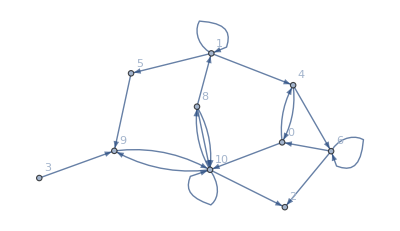
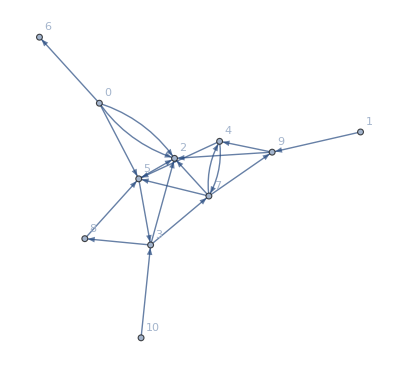
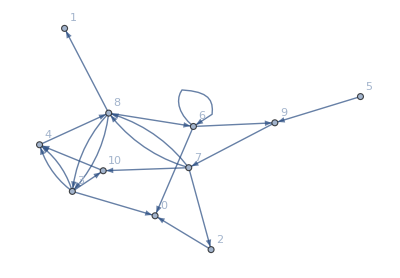
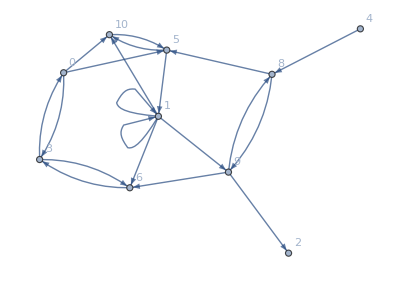
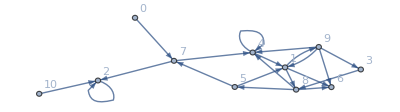
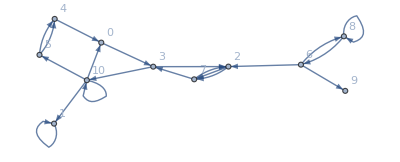
CommunityGraphPlot[{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}]

```mathematica
CommunityGraphPlot[Out[90]]
```

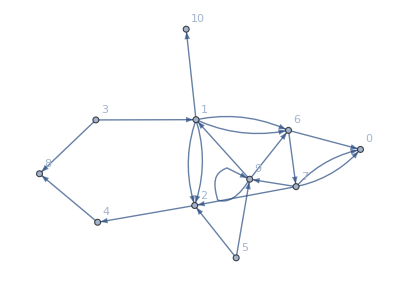

```mathematica
GFunction[10, 20]
```

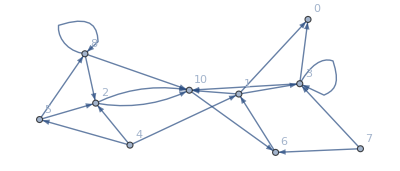
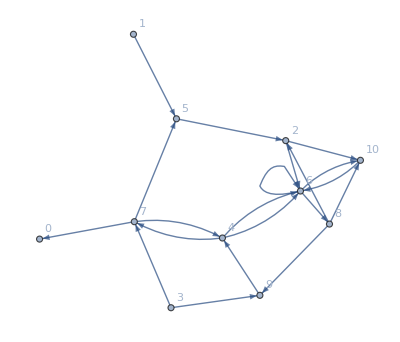
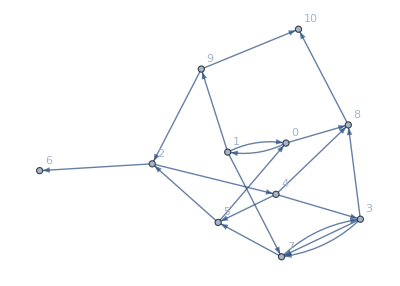
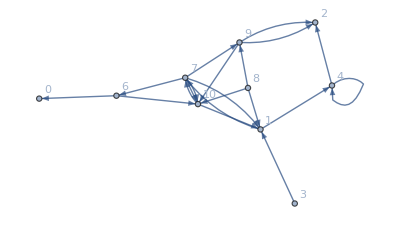
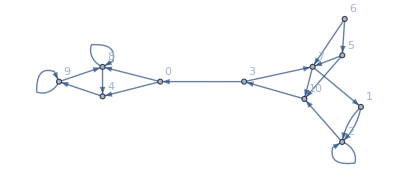
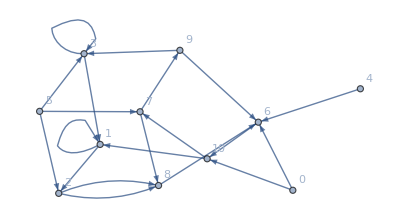

```mathematica
Table[Graph[GFunction[10, 20]],6]
```

```mathematica
MultipleGFunction[numNodes_, numEdges_, numGraphs_] :=Table[Graph[GFunction[numNodes,numEdges]],numGraphs]
```

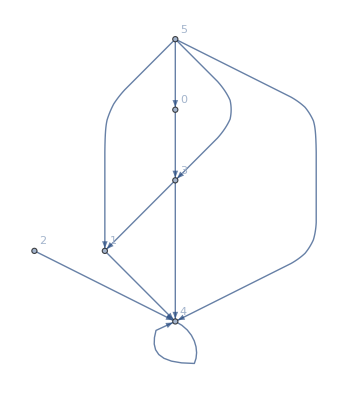
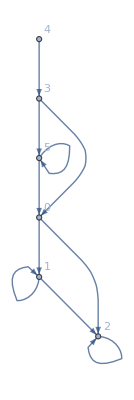
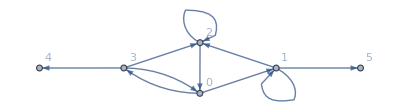
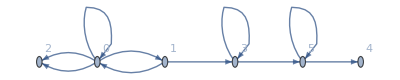
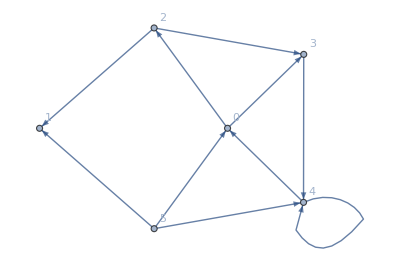
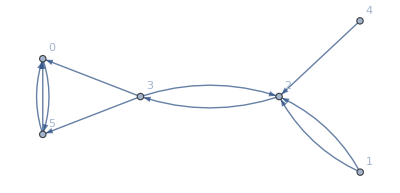
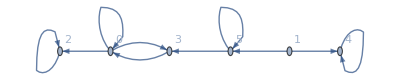
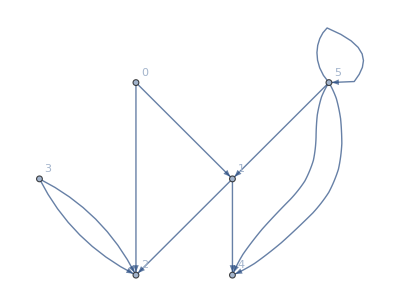

```mathematica
MultipleGFunction[5, 10, 10]
```

```mathematica
CommunityGraphPlot[GFunction[5, 10]]
```

-Graphics-

```mathematica
Table[CommunityGraphPlot[GFunction[5, 10]], 6]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CGraph[numNodes_, numEdges_] := CommunityGraphPlot[GFunction[numNodes, numEdges]]
```

```mathematica
Table[CGraph[10, 30], 10]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CommunityGraphPlot[Graph[{1<->2,2<->3,3<->1},EdgeWeight->{_?(OddQ[First[10]]&)->-1}, EdgeLabels->"Name"]]
```

First::normal: Nonatomic expression expected at position 1 in First[10].

CommunityGraphPlot[Graph[{1<->2,2<->3,3<->1},EdgeWeight→{_?(OddQ[First[10]]&)→-1},EdgeLabels→Name]]

```mathematica
TransitiveClosureGraph[GFunction[10, 30]]
```

TransitiveClosureGraph::graph: A graph object is expected at position 1 in TransitiveClosureGraph[GFunction[10,30]].

```mathematica
TransitiveClosureGraph[Graph[Table[RandomInteger[numNodes]->RandomInteger[numNodes],numEdges],VertexLabels->All]]
```

Table::nliter: Non-list iterator numEdges at position 2 does not evaluate to a real numeric value.

TransitiveClosureGraph::graph: A graph object is expected at position 1 in TransitiveClosureGraph[Graph[Table[RandomInteger[numNodes]→RandomInteger[numNodes],numEdges],VertexLabels→All]].

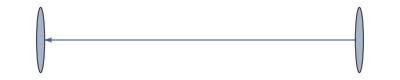

```mathematica
TransitiveClosureGraph[Graph[RandomInteger[10]->RandomInteger[30]]]
```

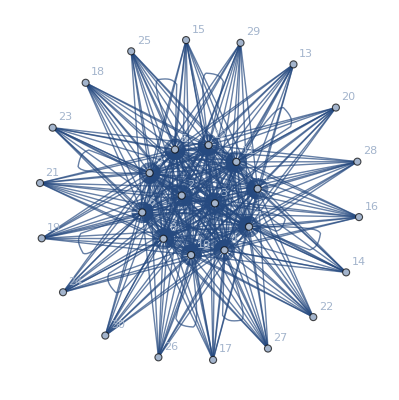

```mathematica
Graph[Flatten[Table[i->j, {i, 3,30}, {j, 12}]], VertexLabels->Automatic]
```

```mathematica
Graph[i->j, {i, 3,30}, {j, 12}]
```

Graph::nonopt: Options expected (instead of {j,12}) beyond position 2 in Graph[i→j,{i,3,30},{j,12}]. An option must be a rule or a list of rules.

```mathematica
Graph[Flatten[Table[i->j, {i, 3,30}, {j, 12}]], VertexLabels->Automatic]
```

-Graphics-

```mathematica
GFunction[5, 10]
```

GFunction[5,10]

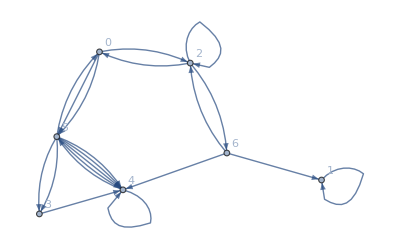

```mathematica
GFunction[6, 20]
```

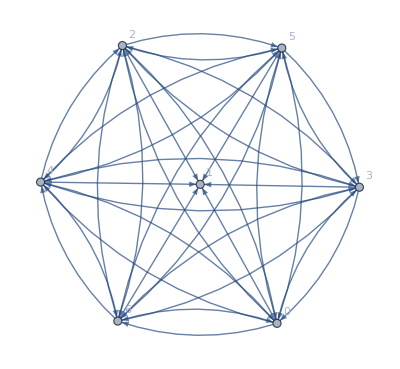

```mathematica
TransitiveClosureGraph[Out[123]]
```

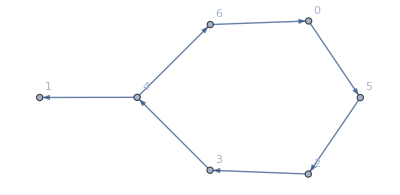

```mathematica
TransitiveReductionGraph[Out[123]]
```

```mathematica
GraphAll[numIterations_, numNodes_, numEdges_] :=Module[
{graph1 := GFunction[numNodes, numEdges]},
Table[{Labeled[graph1, "Original Graph"],
Labeled[TransitiveReductionGraph[graph1], "Transitive Reduction Graph"],
Labeled[TransitiveClosureGraph[graph1], "Transitive Closure Graph"],Labeled[FindSpanningTree[graph1], "Find Spanning Tree"],
Labeled[UndirectedGraph[graph1], "Undirected Graph"],
Labeled[ReverseGraph[graph1], "Reverse Graph"],
Labeled[SimpleGraph[graph1], "Simple Graph"],
Labeled[IndexGraph[graph1], "Index Graph"]}, numIterations]]
```

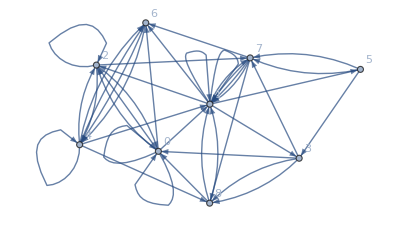
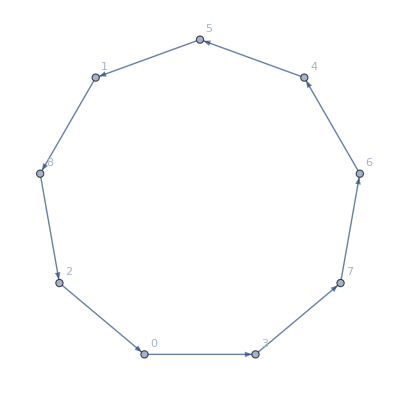
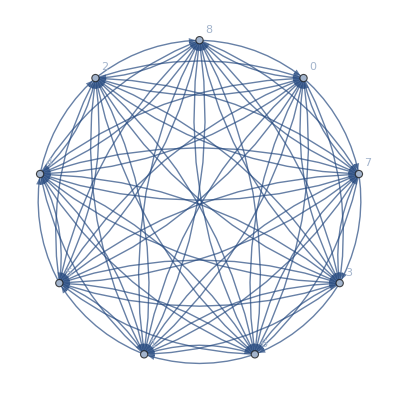
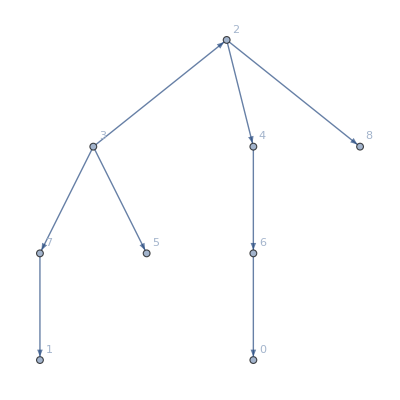
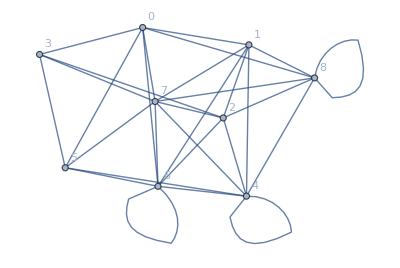
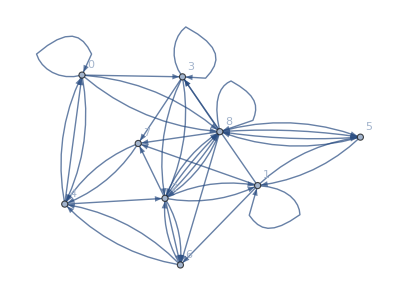
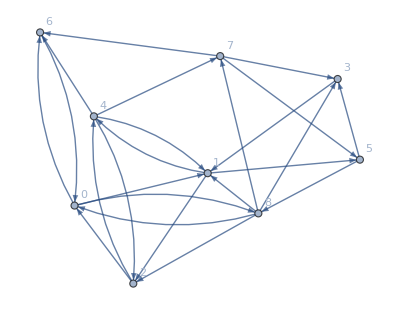
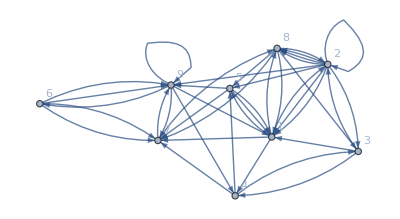
{{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph},{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph},{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph}}

```mathematica
GraphAll[3, 8, 40]
```

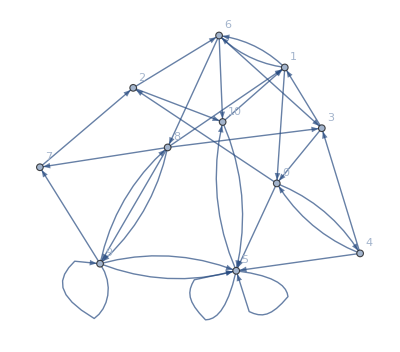
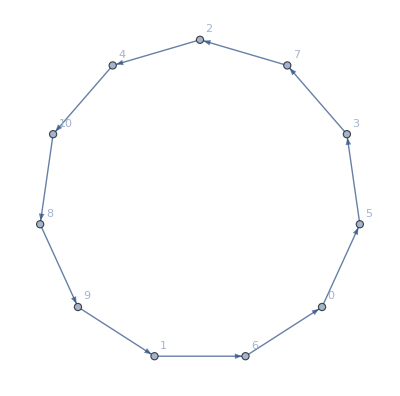
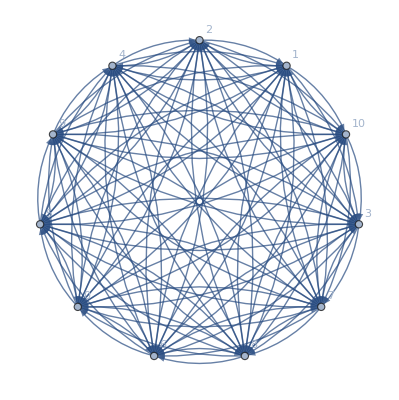
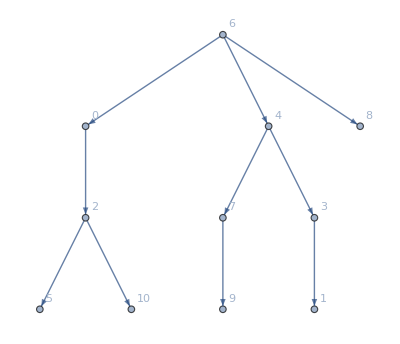
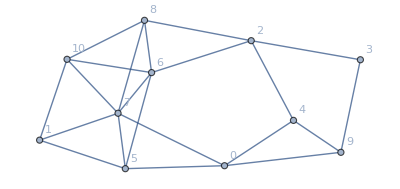
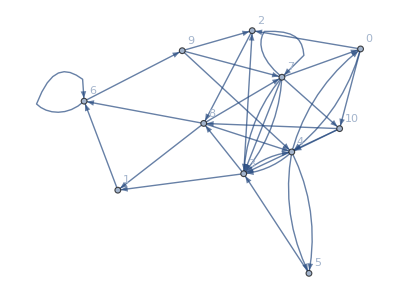
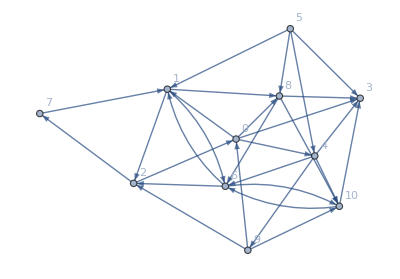
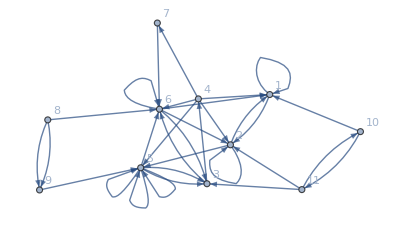
{{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph},{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph}}

```mathematica
GraphAll[2, 10, 32]
```

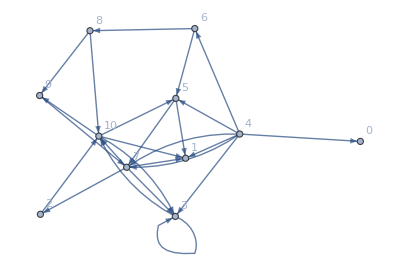
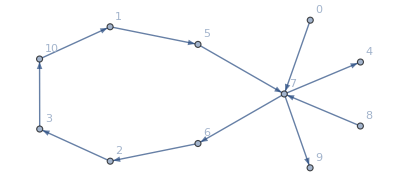
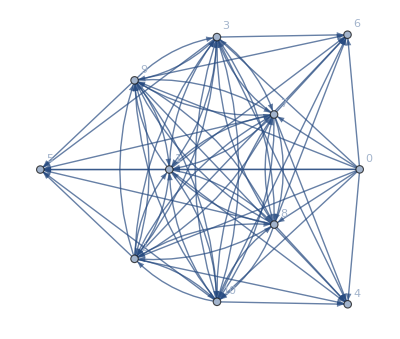
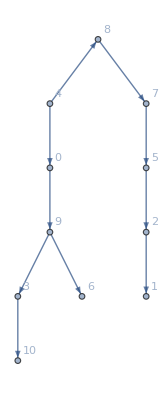
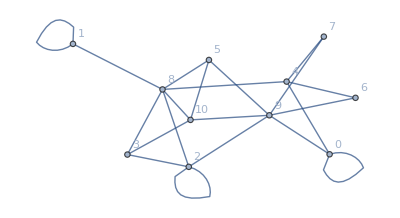
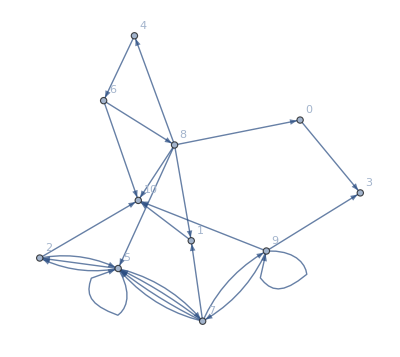
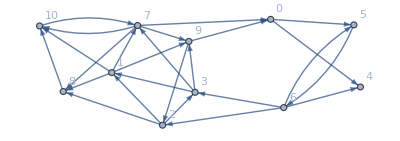
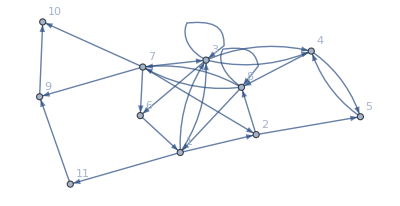
{{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph},{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph}}

```mathematica
GraphAll[2, 10, 25]
```

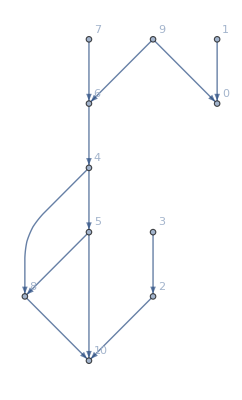
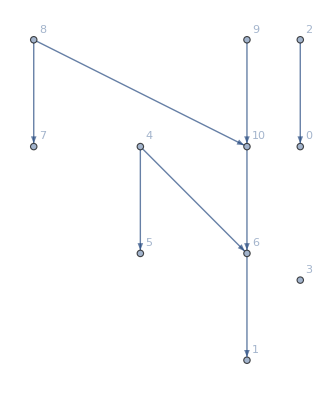
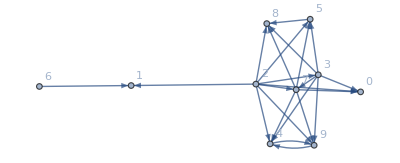
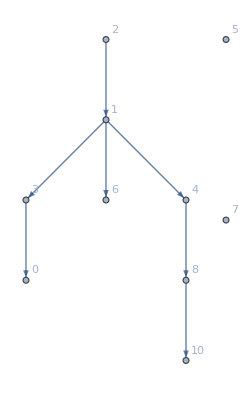
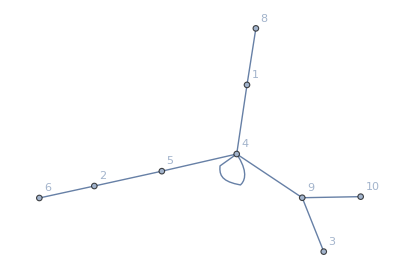
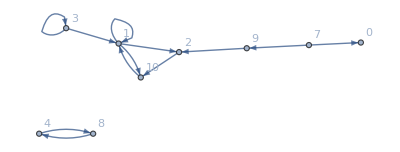
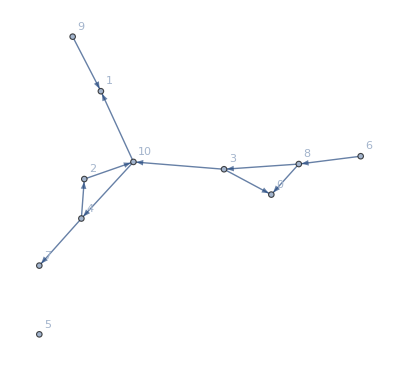
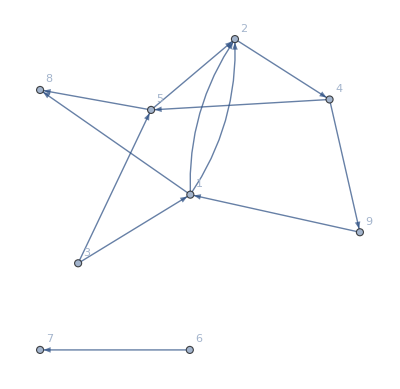
{{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph}}

```mathematica
GraphAll[1, 10, 12]
```

```mathematica
Reverse/@%179
```

{{-Graphics-Index Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Original Graph}}

```mathematica
Flatten[%180]
```

{-Graphics-Index Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Original Graph}

```mathematica
Subsets[Sort[%181]]
```

{{},{-Graphics-Index Graph},{-Graphics-Undirected Graph},{-Graphics-Reverse Graph},{-Graphics-Find Spanning Tree},{-Graphics-Transitive Closure Graph},{-Graphics-Original Graph},{-Graphics-Simple Graph},{-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph},{-Graphics-Undirected Graph,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph},{-Graphics-Reverse Graph,-Graphics-Original Graph},{-Graphics-Reverse Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph},{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph}}

```mathematica
Flatten[%182]
```

{-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph,-Graphics-Index Graph,-Graphics-Undirected Graph,-Graphics-Reverse Graph,-Graphics-Find Spanning Tree,-Graphics-Transitive Closure Graph,-Graphics-Original Graph,-Graphics-Simple Graph,-Graphics-Transitive Reduction Graph}

```mathematica
FunctionX[a_, b_, c_] := Module[{m = a*b-c, n = c^b}, m * n - 12]
```

```mathematica
FunctionX[1, 2, 3]
```

-21